# Setup

```mathematica
Get["C:\\Users\\Miguel\\Github\\libs\\QMB\\Kernel\\init.m"];
```

[QMB Update] A newer version is available (Local: 2.4.1, Remote: 2.4.2).

[QMB Update] Pull updates from GitHub for newest version.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Get["C:\\Users\\Miguel\\Github\\Spin transport\\Quantum channel\\QMB_offline.wl"];*)
```

```mathematica
LaunchKernels[14];
```

# Efficient

## Definitions

```mathematica
(* ================================================================ *)
(* BLOCK 0 — Kernel setup                                           *)
(* ================================================================ *)
(* Set compile target for all Compile calls in this session.        *)
(* Falls back to "WVM" automatically if no C compiler is found.     *)
$CompileTarget = "WVM";
```

```mathematica
(* ================================================================ *)
(* BLOCK 1 — Compiled partial traces (hardcoded for 4x4 ρ_AB)      *)
(*                                                                   *)
(* These are exact index operations on a 4x4 complex matrix.        *)
(* Layout assumed: rows/cols indexed as (q1,q2) ∈ {00,01,10,11}.   *)
(* ================================================================ *)
Clear[TraceOutA,TraceOutB];
TraceOutB = Compile[                  (* keep spin A, trace out B *)
  {{ρ, _Complex, 2}},
  {{ρ[[1,1]] + ρ[[2,2]],  ρ[[1,3]] + ρ[[2,4]]},
   {ρ[[3,1]] + ρ[[4,2]],  ρ[[3,3]] + ρ[[4,4]]}},
  CompilationTarget -> $CompileTarget,
  RuntimeOptions -> "Speed"
];
TraceOutA = Compile[                  (* keep spin B, trace out A *)
  {{ρ, _Complex, 2}},
  {{ρ[[1,1]] + ρ[[3,3]],  ρ[[1,2]] + ρ[[3,4]]},
   {ρ[[2,1]] + ρ[[4,3]],  ρ[[2,2]] + ρ[[4,4]]}},
  CompilationTarget -> $CompileTarget,
  RuntimeOptions -> "Speed"
];
```

```mathematica
(* ================================================================ *)
(* BLOCK 2 — Von Neumann entropy                                     *)
(*                                                                   *)
(* 2×2: compiled with analytical eigenvalues — no Eigenvalues call. *)
(* Eigenvalues of {{a,b},{c,d}} with a,d real and c=Conj[b]:        *)
(*   λ_{1,2} = ((a+d) ± sqrt((a-d).b2 + 4|b|.b2)) / 2                  *)
(*                                                                   *)
(* 4×4: cannot be compiled — Eigenvalues[] is not compilable.       *)
(*  Called once per time step on a 4×4 matrix — cost is negligible. *)
(* ================================================================ *)
Clear[VNEntropy2x2,VNEntropy4x4];
VNEntropy2x2 = Compile[
  {{ρ, _Complex, 2}},
  Module[{r11, r22, r12r, r12i, absq, disc, λ1, λ2},
    r11  = Re[ρ[[1,1]]];
    r22  = Re[ρ[[2,2]]];
    r12r = Re[ρ[[1,2]]];
    r12i = Im[ρ[[1,2]]];
    absq = r12r^2 + r12i^2;               (* |ρ12|.b2 — never negative *)
    disc = Sqrt[(r11 - r22)^2 + 4.*absq]; (* sqrt arg always ≥ 0     *)
    λ1   = (r11 + r22 + disc)/2.;
    λ2   = (r11 + r22 - disc)/2.;
    If[λ1 > 1.*^-14, -λ1*Log[λ1], 0.] +
    If[λ2 > 1.*^-14, -λ2*Log[λ2], 0.]
  ],
  CompilationTarget -> $CompileTarget,
  RuntimeOptions -> "Speed"
];
VNEntropy4x4[ρ_] := Module[
  {λ = Select[Re[Eigenvalues[N[ρ]]], # > 1.*^-14 &]},
  -λ . Log[λ]
];
```

```mathematica
(* ================================================================ *)
(* BLOCK 3 — Concurrence (Wootters 1998)                            *)
(*                                                                   *)
(* spinFlip = σy⊗σy is constant — precomputed once here as a        *)
(* packed numerical array so Dot calls use BLAS.                    *)
(* Eigenvalues on 4x4 is not compilable; the 4x4 call is trivial.   *)
(* ================================================================ *)
spinFlip = N[KroneckerProduct[PauliMatrix[2], PauliMatrix[2]]];

Clear[Concurrence];
Concurrence[ρ_] := Module[
  {ρTilde, λs},
  ρTilde = spinFlip . Conjugate[ρ] . spinFlip;
  λs     = Reverse[Sort[Re[Sqrt[Chop[Eigenvalues[ρ . ρTilde]]]]]];
  Max[0., λs[[1]] - λs[[2]] - λs[[3]] - λs[[4]]]
];
```

```mathematica
(* ================================================================ *)
(* BLOCK 4 — Single-pass observable aggregator                      *)
(*                                                                   *)
(* Takes the 4×4 ρ_AB and a reference state ρ_ref (for survival).  *)
(* All quantities computed in one pass over ρ_AB — no redundancy.   *)
(* ================================================================ *)
Clear[ComputeAllObservables];
ComputeAllObservables[ρAB_, ρref_] := Module[
  {ρA, ρB, SA, SB, SAB},
  ρA  = TraceOutB[ρAB];
  ρB  = TraceOutA[ρAB];
  SA  = VNEntropy2x2[ρA];
  SB  = VNEntropy2x2[ρB];
  SAB = VNEntropy4x4[ρAB];
  <|
    "Concurrence"  -> Concurrence[ρAB],
    "Purity"       -> Re[Tr[ρAB . ρAB]],
    "EntropyA"     -> SA,
    "EntropyB"     -> SB,
    "MutualInfo"   -> SA + SB - SAB,       (* I(A:B) = S(A)+S(B)-S(AB) *)
    "SpinSurvival" -> Re[Tr[ρref . ρAB]]   (* valid for pure ρref      *)
  |>
];
```

```mathematica
(* ================================================================ *)
(* BLOCK 5 — Transfer tensor builder                                *)
(*                                                                   *)
(* Given eigenvector matrix U (rows = eigenvectors) and chain       *)
(* length L, returns a {2,2,2,2} array of (D×D) matrices where      *)
(*                                                                   *)
(*  T[[q1+1,q2+1,q1p+1,q2p+1]]_αβ                                  *)
(*    = Σ_c Conj[U[[α, idx(q1,c,q2)]]] * U[[β, idx(q1p,c,q2p)]]   *)
(*                                                                   *)
(* idx(q1,c,q2) is the linear index in the [Q1, Chain, Q2] layout. *)
(*                                                                   *)
(* In matrix form: T = Conj[U[:,colsA]] . Transpose[U[:,colsB]]    *)
(* — a (D×2^L)·(2^L×D) product using BLAS.                         *)
(*                                                                   *)
(* The 16 products are independent -> parallelize over them.         *)
(* ================================================================ *)
Clear[BuildTransferTensors];
BuildTransferTensors[U_, L_] := Module[
  {dC, idxFull, getCols},
  dC       = 2^L;
  idxFull  = Compile[{{q1,_Integer},{c,_Integer},{q2,_Integer},{dC,_Integer}},
               q1*(2*dC) + c*2 + q2 + 1,
               CompilationTarget -> $CompileTarget];
  getCols[q1_, q2_] := Table[idxFull[q1, c, q2, dC], {c, 0, dC - 1}];
  ParallelTable[
    Conjugate[U[[All, getCols[q1, q2]]]] . Transpose[U[[All, getCols[q1p, q2p]]]],
    {q1, 0, 1}, {q2, 0, 1}, {q1p, 0, 1}, {q2p, 0, 1}
  ]
];
```

```mathematica
(* ================================================================ *)
(* BLOCK 6 — K-matrix builder                                       *)
(*                                                                   *)
(* Absorbs ρ_E (energy-basis initial state) into the transfer       *)
(* tensors. Result shape: {4, 4, D.b2}.                               *)
(*                                                                   *)
(*  K[[i,j,p]] = (ρ_E ⊙ T_ij)_flat[p]                              *)
(*                                                                   *)
(* At each time step: ρ_AB(t) = K . phase_flat(t)  [4×4 matrix]    *)
(* This single BLAS call replaces all the per-step matrix work.     *)
(* ================================================================ *)
Clear[BuildKMatrix];
BuildKMatrix[ρE_, T_] := ArrayReshape[
  Table[
    Flatten[ρE * T[[q1+1, q2+1, q1p+1, q2p+1]]],
    {q1, 0, 1}, {q2, 0, 1}, {q1p, 0, 1}, {q2p, 0, 1}
  ],
  {4, 4, Length[ρE]^2}
];
```

```mathematica
(* ================================================================ *)
(* BLOCK 7 — Energy difference vector and global survival vector    *)
(*                                                                   *)
(* dEflat[[α*(D)+β]] = E_α - E_β  (real packed array, length D.b2)   *)
(*                                                                   *)
(* Gflat encodes the global survival probability as a dot product:  *)
(*  surv_global(t) = Re[ Gflat . Conj[phase_flat(t)] ]             *)
(*                                                                   *)
(* Derivation: Tr[ρ0·ρ(t)] = Tr[ρ_E · ρ_E(t)]                     *)
(*  = Σ_αβ ρ_E_αβ · ρ_E_βα · e^{+i(E_α-E_β)t}                     *)
(*  = Gflat · Conj[phase_flat]    (Conj because sign flips)         *)
(* ================================================================ *)
Clear[BuildEnergyDiffs,BuildGflat];
BuildEnergyDiffs[E_] := Flatten[Outer[Subtract, E, E]];   (* D.b2-vector, real *)
BuildGflat[ρE_] := Flatten[ρE * Transpose[ρE]];           (* D.b2-vector, complex *)
```

```mathematica
(* ================================================================ *)
(* BLOCK 8 — Core per-step functions                                *)
(*                                                                   *)
(* These are the only functions called inside the time loop.        *)
(* ComputeRhoAB: one Exp on a packed array + one BLAS Dot.          *)
(* ComputeSurvivalGlobal: one Exp + one dot product (scalar result).*)
(* ================================================================ *)
Clear[ComputeRhoAB,ComputeSurvivalGlobal];
ComputeRhoAB[Kmat_, dEflat_, t_?NumericQ] :=
  Kmat . Exp[(-I) * dEflat * t];
ComputeSurvivalGlobal[Gflat_, dEflat_, t_?NumericQ] :=
  Re[Gflat . Conjugate[Exp[(-I) * dEflat * t]]];
```

## Hamiltonian and couplings

```mathematica
(* ================================================================ *)
(* BLOCK 9 — Pauli operators                                        *)
(* Packed numerical arrays — no symbolic overhead anywhere          *)
(* ================================================================ *)
σx  = N[PauliMatrix[1]];
σy  = N[PauliMatrix[2]];
σz  = N[PauliMatrix[3]];
σp  = σx + I*σy;   (* raising  operator *)
σm  = σx - I*σy;   (* lowering operator *)
id2 = N[IdentityMatrix[2]];
```

```mathematica
(* ================================================================ *)
(* BLOCK 10 — Hamiltonian embedding functions                       *)
(*                                                                   *)
(* All operators live in the full [Q1, Chain, Q2] Hilbert space.    *)
(* SparseArray identities keep construction memory-efficient.       *)
(* Normal[] called only once at diagonalization — not here.         *)
(* ================================================================ *)
Clear[SparseId,EmbedSpinA,EmbedSpinB,EmbedChain,EmbedChainSite];
SparseId[n_] := SparseArray[Band[{1, 1}] -> 1., {n, n}];

(* Embed a 2×2 operator at spin A position in the full space *)
EmbedSpinA[op_, L_] :=
  KroneckerProduct[op, SparseId[2^L], SparseId[2]];
(* Embed a 2×2 operator at spin B position in the full space *)
EmbedSpinB[op_, L_] :=
  KroneckerProduct[SparseId[2], SparseId[2^L], op];
(* Embed the full chain Hamiltonian block in the full space *)
EmbedChain[Ha_, L_] :=
  KroneckerProduct[SparseId[2], Ha, SparseId[2]];
(* Embed a 2×2 operator at site k (1-indexed) within the chain     *)
(* Useful for chain-internal interactions if building Ha manually   *)
EmbedChainSite[op_, k_, L_] :=
  KroneckerProduct[SparseId[2^(k - 1)], op, SparseId[2^(L - k)]];
```

```mathematica
(* ================================================================ *)
(* BLOCK 11 — Boundary coupling constructors                        *)
(*                                                                   *)
(* Takes a list of {opLeft, opRight} pairs and coupling strength λ. *)
(* Each pair contributes one term in the interaction Hamiltonian.   *)
(*                                                                   *)
(* couplingTerms format: a list of {opA, opChainEdge} pairs.        *)
(*                                                                   *)
(* Examples:                                                         *)
(*   Heisenberg: λ*{{σx,σx},{σy,σy},{σz,σz}}                       *)
(*   Flip-flop:  λ*{{σp,σm},{σm,σp}}                               *)
(*   Ising:      λ*{{σz,σz}}                                        *)
(*                                                                   *)
(* A-chain couples spin A to the FIRST chain site.                  *)
(* B-chain couples spin B to the LAST  chain site.                  *)
(* ================================================================ *)
Clear[BuildCouplingAChain, BuildCouplingBChain];

BuildCouplingAChain[couplingTerms_, L_] := Sum[
  term[[1]] * KroneckerProduct[
    term[[2]],
    KroneckerProduct[term[[3]], SparseId[2^(L - 1)]],
    SparseId[2]
  ],
  {term, couplingTerms}
];

BuildCouplingBChain[couplingTerms_, L_] := Sum[
  term[[1]] * KroneckerProduct[
    SparseId[2],
    KroneckerProduct[SparseId[2^(L - 1)], term[[2]]],
    term[[3]]
  ],
  {term, couplingTerms}
];
```

```mathematica
(* ================================================================ *)
(* BLOCK 12 — Full Hamiltonian assembler and diagonalization        *)
(*                                                                   *)
(* Ha is passed as a precomputed 2^L × 2^L numerical matrix.        *)
(* The model (Ising, XXZ, ...) lives entirely inside Ha.            *)
(* The coupling topology lives in couplingA, couplingB.             *)
(* This is the ONLY place density is needed — for LAPACK.           *)
(* Returns {eigenvalues (D-vector), eigenvectors (D×D, rows=vecs)}  *)
(* ================================================================ *)
Clear[BuildFullHamiltonian,DiagonalizeH];
BuildFullHamiltonian[HAlocal_, Ha_, HBlocal_, couplingA_, couplingB_, L_] :=
  EmbedSpinA[HAlocal, L] +
  EmbedChain[Ha, L]        +
  EmbedSpinB[HBlocal, L]  +
  BuildCouplingAChain[couplingA, L] +
  BuildCouplingBChain[couplingB, L];

DiagonalizeH[HT_] := Transpose[Sort[Transpose[Eigensystem[Normal[N[HT]]]]]];
```

```mathematica
(* ================================================================ *)
(* BLOCK 13 — Initial state construction                            *)
(*                                                                   *)
(* The Hamiltonian lives in [Q1, Chain, Q2] space.                  *)
(*                                                                   *)
(* CASE A — correlated spin state (Bell, Werner, etc.):             *)
(*   ρ_AB ⊗ ρ_chain builds naturally as [Q1,Q2,Chain].              *)
(*   Needs a tensor index permutation -> [Q1,Chain,Q2].              *)
(*   Done by reshaping to rank-6, transposing, reshaping back.      *)
(*   Pure index operation — ZERO arithmetic.                         *)
(*                                                                   *)
(* CASE B — fully factored ρ_A ⊗ ρ_chain ⊗ ρ_B:                    *)
(*   KroneckerProduct in this order directly gives [Q1,Chain,Q2].   *)
(*   NO permutation needed.                                          *)
(* ================================================================ *)
(* Tensor permutation [Q1,Q2,Chain] -> [Q1,Chain,Q2]                *)
(* Rank-6 index map: {q1,q2,c,q1',q2',c'} -> {q1,c,q2,q1',c',q2'} *)
(* Transpose argument: position k gets the index that was at perm[k]*)
Clear[PermuteToQ1ChainQ2,BuildInitialStateCorrelated,BuildInitialStateProduct];
PermuteToQ1ChainQ2[ρ_, L_] := Module[{dC = 2^L},
  ArrayReshape[
    Transpose[
      ArrayReshape[ρ, {2, 2, dC, 2, 2, dC}],
      {1, 3, 2, 4, 6, 5}
    ],
    {4*dC, 4*dC}
  ]
];
(* Case A: spin state correlated (4×4) + chain state (2^L × 2^L)   *)
BuildInitialStateCorrelated[ρAB_, ρchain_, L_] :=
  PermuteToQ1ChainQ2[N[KroneckerProduct[ρAB, ρchain]], L];
(* Case B: fully factored — no permutation                          *)
BuildInitialStateProduct[ρA_, ρchain_, ρB_] :=
  N[KroneckerProduct[ρA, ρchain, ρB]];
```

```mathematica
(* ================================================================ *)
(* BLOCK 14 — Energy basis projection                               *)
(* ρ_E = U · ρ0 · U†                                                *)
(* ================================================================ *)
Clear[ProjectToEnergyBasis];
ProjectToEnergyBasis[U_, ρ0_] := U . ρ0 . ConjugateTranspose[U];
```

```mathematica
(* ================================================================ *)
(* DISTRIBUTE — send all definitions to parallel kernels            *)
DistributeDefinitions[
  σx, σy, σz, σp, σm, id2, spinFlip,
  TraceOutA, TraceOutB, VNEntropy2x2, VNEntropy4x4, Concurrence,
  ComputeAllObservables, ComputeRhoAB, ComputeSurvivalGlobal
];
```

## Parameters

```mathematica
(* ================================================================ *)
(* MODEL + STATE SPECIFICATION                                      *)
(* This is the only block you change between runs.                  *)
(* ================================================================ *)
(* --- System size and time grid --- *)
L   =6;
```

```mathematica
{Δa,Δb,λa,λb}={1,1,0.35,0.35};
```

```mathematica
(* --- Local Hamiltonians for the two system spins ---             *)
HAlocal = Δa * σz;       (* 2×2, field on spin A *)
HBlocal = Δb * σz;       (* 2×2, field on spin B *)
(* --- Boundary coupling terms ---                                  *)
(* Format: list of {opLeft, opRight} pairs, scaled by λ            *)
(* Each pair becomes one term in the interaction Hamiltonian.      *)
couplingA={{λa,σp,σm},{λa,σm,σp}};
couplingB={{λb,σp,σm},{λb,σm,σp}};(* flip-flop chain↔B  *)
```

```mathematica
?QMB`*
```

```mathematica
?QubitStateFromBlochVector
```

```mathematica
?XXZwLocalDefectHamiltonian
```

```mathematica
{h1,h2}={0,0};
```

```mathematica
{Jxy,Jz,w,ed,d,L}={1.,0.5,0,0,L,8};
```

```mathematica
(* --- Chain Hamiltonian (your choice of model) ---               *)
(* Pass a precomputed numerical 2^L × 2^L matrix.                  *)
(* Example: XXZ chain with anisotropy Δ, boundary fields h1, h2    *)
Ha = XXZwLocalDefectHamiltonian[Jxy, Jz, w, ed, L, d];
```

```mathematica
(* --- Build and diagonalize the full Hamiltonian --- *)
HT             = Chop[BuildFullHamiltonian[HAlocal, Ha, HBlocal, couplingA, couplingB, L]];
{Eval, Evec}   = DiagonalizeH[HT];
```

```mathematica
MeanLevelSpacingRatio[Sort[Chop[Eval]]]
```

0.199777

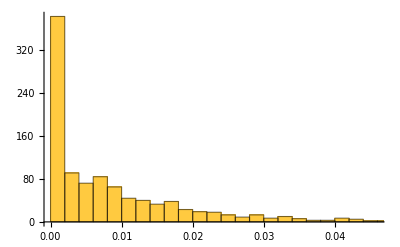
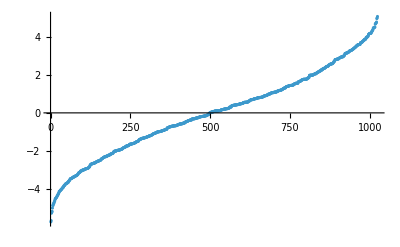

```mathematica
{Histogram[Differences[Sort[Chop[Eval]]]],ListPlot[Sort[Chop[Eval]]]}
```

```mathematica
(* --- Initial state --- *)
(* Option A: Bell state on spins, coherent state on chain          *)
bellState = {1, 0, 0, 1} / Sqrt[2.];
rhoAB     = Outer[Times, bellState, Conjugate[bellState]];
rhoChain  = Dyad[coherentstate[QubitStateFromBlochVector[0., 0], L]];
rho0      = BuildInitialStateCorrelated[rhoAB, rhoChain, L];
(* reference for spin survival *)
rhoABref  = rhoAB;
```

```mathematica
(* Option B: fully factored state — swap the two lines above with: *)
(* rho0     = BuildInitialStateProduct[rhoA, rhoChain, rhoB];      *)
(* rhoABref = KroneckerProduct[rhoA, rhoB];                        *)
```

## Method

```mathematica
(* ================================================================ *)
(* BLOCK 15 — Precomputation sequence                               *)
(* Required inputs already defined upstream:                        *)
(*   {Eval, Evec}  from DiagonalizeH[HT]                           *)
(*   rho0          from BuildInitialState(Correlated|Product)[...]  *)
(*   rhoABref      4×4 reference spin state (for survival)         *)
(*                 = rhoAB for correlated case                      *)
(*                 = KroneckerProduct[rhoA, rhoB] for product case  *)
(* ================================================================ *)
Clear[rhoE,Tmat,Kmat,dEflat,Gflat];
rhoE   = ProjectToEnergyBasis[Evec, rho0];      (* D×D, computed ONCE    *)
Tmat   = BuildTransferTensors[Evec, L];          (* {2,2,2,2} of D×D mats *)
Kmat   = BuildKMatrix[rhoE, Tmat];               (* {4,4,D.b2} — core object *)

Clear[Tmat];                                     (* no longer needed       *)
dEflat = BuildEnergyDiffs[Chop[Eval]];                 (* D.b2-vector, real        *)
Gflat  = BuildGflat[rhoE];                      (* D.b2-vector, complex     *)
```

```mathematica
(* ================================================================ *)
(* BLOCK 16 — Distribute heavy objects to parallel kernels          *)
(*                                                                   *)
(* Done explicitly AFTER precomputation so workers receive the      *)
(* final packed arrays directly.                                    *)
(* DistributedContexts -> None in the loop avoids a second          *)
(* automatic distribution pass on every ParallelTable call.         *)
(*                                                                   *)
(* Memory note: each worker receives its own copy of Kmat.          *)
(*   L=7  (D=512)  -> ~32 MB × n_kernels                            *)
(*   L=9  (D=2048) -> ~512 MB × n_kernels  ← verify RAM before use  *)
(* ================================================================ *)
DistributeDefinitions[
  Kmat, dEflat, Gflat, rhoABref,
  spinFlip,
  TraceOutA, TraceOutB,
  VNEntropy2x2, VNEntropy4x4,
  Concurrence,
  ComputeAllObservables,
  ComputeRhoAB,
  ComputeSurvivalGlobal
];
```

```mathematica
(* ================================================================ *)
(* BLOCK 17 — Time evolution loop                                   *)
(* Per step cost:                                                    *)
(*   1. Exp on D.b2-vector    -> packed array op, no loop              *)
(*   2. Kmat . phaseVec     -> BLAS (4×4×D.b2)·(D.b2) = 4×4 matrix      *)
(*   3. All observables     -> from 4×4 ρAB only                     *)
(*                                                                   *)
(* tMax and dt are free parameters — set them before this block.    *)
(* ================================================================ *)
tMax=50.;
dt=0.1;
tlist = Range[0., tMax, dt];                (* set tMax, dt upstream *)

AbsoluteTiming[allResults = ParallelTable[
  Module[{rhoAB, survGlobal, obs},
    rhoAB      = Chop[ComputeRhoAB[Kmat, dEflat, t]];
    survGlobal = ComputeSurvivalGlobal[Gflat, dEflat, t];
    obs        = ComputeAllObservables[rhoAB, rhoABref];
    Join[<|"Time" -> t, "SurvivalGlobal" -> survGlobal|>, obs]
  ],
  {t, tlist},
  DistributedContexts -> None        (* already distributed in Block 16 *)
];]
```

{70.1937,Null}

```mathematica
(* ================================================================ *)
(* BLOCK 18 — Result extraction                                     *)
(* allResults is a list of Associations, one per time step.         *)
(* Available keys:                                                   *)
(*   "Time", "SurvivalGlobal",                                      *)
(*   "Concurrence", "Purity",                                       *)
(*   "EntropyA", "EntropyB", "MutualInfo", "SpinSurvival"           *)
(* ================================================================ *)
Clear[ExtractTimeSeries];
ExtractTimeSeries[key_] :=
  {#["Time"], #[key]} & /@ allResults;
```

## Results

```mathematica
allResults[[1]]
(* <| "Time" -> 0., "SurvivalGlobal" -> 1., "Concurrence" -> 1., 
      "Purity" -> 1., "EntropyA" -> 0., "EntropyB" -> 0., 
      "MutualInfo" -> 0., "SpinSurvival" -> 1. |> *)
```

<|Time→0.,SurvivalGlobal→1.,Concurrence→1.,Purity→1.,EntropyA→0.693147,EntropyB→0.693147,MutualInfo→1.38629,SpinSurvival→1.|>

```mathematica
(* ExtractTimeSeries["key"] gives {{t0,v0},{t1,v1},...} ready to plot *)
ListLinePlot[ExtractTimeSeries["Concurrence"],
  Frame -> True, FrameLabel -> {"Time (t)", "Concurrence"},
LabelStyle->Directive[Black,20],
  PlotStyle -> {Thick, Red}, ImageSize -> 600]

ListLinePlot[ExtractTimeSeries["SpinSurvival"],
  Frame -> True, FrameLabel -> {"Time (t)", "1st Spin Survival"},
LabelStyle->Directive[Black,20],
  PlotStyle -> {Thick, Blue}, ImageSize -> 600,PlotRange->All]

ListLinePlot[ExtractTimeSeries["MutualInfo"],
  Frame -> True, FrameLabel -> {"Time (t)", "Mutual Information"},
LabelStyle->Directive[Black,20],
  PlotStyle -> {Thick, Purple}, ImageSize -> 600,PlotRange->All]
```

```mathematica
ListLinePlot[
  {ExtractTimeSeries["SpinSurvival"],
   ExtractTimeSeries["Concurrence"],
   ExtractTimeSeries["Purity"],
   ExtractTimeSeries["EntropyA"],
   ExtractTimeSeries["EntropyB"],
   ExtractTimeSeries["MutualInfo"]},
  Frame -> True,
  FrameLabel -> {"Time (t)", "Observables"},
  LabelStyle -> Directive[Black, 16],
  PlotStyle -> {
    Directive[Thick, Blue],
    Directive[Thick, Red],
    Directive[Thick, Darker[Green], Dashed],
    Directive[Thick, Orange],
    Directive[Thick, Purple],
    Directive[Thick, Darker[Red], DotDashed]
  },
  PlotLegends -> Placed[
    LineLegend[
      {"Spin Survival", "Concurrence", "Purity",
       "Entropy A", "Entropy B", "Mutual Info"},
      LegendFunction -> Framed
    ],
    Right
  ],
  ImageSize -> 700
]
```

# Choi